```mathematica
sol1=DSolve[{D[y[x,t],t]+2 D[y[x,t],x]==Sin[x],y[0,t]==Cos[t]},y[x,t],{x,t}]
Plot3D[y[x,t]/.sol1,{x,-10,10},{t,-10,10}]
```

{{y[x,t]→1/2 (1+2 Cos[1/2 (2 t-x)]-Cos[x])}}

-Graphics3D-

```mathematica
pdesol=DSolve[{b D[y[x,t],t]+a D[y[x,t],x]==c Sin[x],y[0,t]==a Cos[t]},y[x,t],{x,t}];
Fsol[x_,t_]=(y[x,t]/.pdesol)[[1]];
Fsol[2,1];
Fsol[2,1]/.{a->2,b->5,c->10};
Plot3D[Fsol[x,t]/.{a->2,b->5,c->10},{x,-10,10},{t,-5,5}]
Manipulate[Plot3D[Fsol[x,t]/.{a->aa,b->bb,c->cc},{x,-4,4},{t,-2,2}],{aa,-2,2},{bb,-2,2},{cc,-2,2},SaveDefinitions->True]
```

-Graphics3D-

```mathematica
nsol1=NDSolve[{D[y[x,t],t]+2 D[y[x,t],x]==3,y[x,0]==x+3,y[5,t]==t+8},y[x,t],{x,0,5},{t,0,4}]
Plot3D[nsol1[[1,1,2]],{x,0,5},{t,0,4}]
```

{{y[x,t]→InterpolatingFunction[{{0., 5.}, {0., 4.}}, <>][x,t]}}

-Graphics3D-

```mathematica
fsol[k_?NumericQ]:=NDSolve[{Derivative[2,0][u][x,t] x^4==x^3 t Cos[x Sin[t]]/(1/10+Sin[t])+k Derivative[0,1][u][x,t],u[0,t]==0,u[1,t]==0,u[x,0]==x (1-x)},u[x,t],{x,0,1},{t,0,1}]
fsol[5];
Plot3D[Evaluate[u[x,t]/.fsol[5][[1]]],{t,0,1},{x,0,1},PlotRange->All]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Evaluate[u[x,t]/.fsol[k][[1]]],{t,0,1},{x,0,1},PlotRange->All],{k,1/100,5},SaveDefinitions->True]
```

```mathematica
NDSolve[{D[u[t, x, y], t, t] == 
   D[u[t, x, y], x, x] + 
    D[u[t, x, y], y, y]/2 + (1 - u[t, x, y]^2) (1 + 2 u[t, x, y]), 
  u[0, x, y] == E^-(x^2 + y^2), u[t, -5, y] == u[t, 5, y], 
  u[t, x, -5] == u[t, x, 5], 
Derivative[1,0,0][u][0, x, y] == 0}, u, {t, 0, 4}, {x, -5, 
  5}, {y, -5, 5}]
Manipulate[Plot3D[Evaluate[u[t, x, y] /. %], {x, -5, 5}, {y, -5, 5}, 
  PlotRange -> All,PlotTheme->"Scientific"], {t, 1, 4}]
```

{{u→InterpolatingFunction[{{0., 4.}, {…, -5., 5., …}, {…, -5., 5., …}}, <>]}}

```mathematica
L=50;
sol=NDSolve[{I D[u[t,x],t]+D[u[t,x],x,x]+2 Abs[u[t,x]]^2 u[t,x]==0.1 (1-Cos[Pi x/L]),u[0,x]==Sech[x] Exp[I x],u[t,-L]==u[t,L]},u,{t,0,10},{x,-L,L}]
Plot3D[Evaluate[Abs[u[t,x]/.First[sol]]],{t,0,10},{x,-L,L},PlotPoints->60,MaxRecursion->3,Mesh->None]
```

NDSolve::eerr: Warning: scaled local spatial error estimate of 565.331 at t = 10. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 541 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

{{u→InterpolatingFunction[{{0., 10.}, {…, -50., 50., …}}, <>]}}

-Graphics3D-

{{y→InterpolatingFunction[{{0., 10.}}, <>]}}

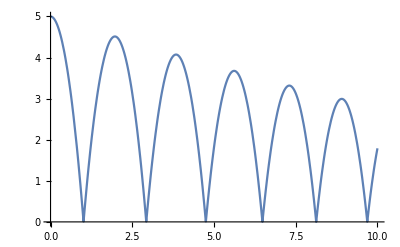

```mathematica
sol=NDSolve[{y''[t]==-9.81,y[0]==5,y'[0]==0,WhenEvent[y[t]==0,y'[t]->-0.95 y'[t]]},y,{t,0,10}]
Plot[y[t]/.sol,{t,0,10}]
```

```mathematica
Clear[f];
f=E^Sin[50 x]+Sin[60 E^y]+Sin[70 Sin[x]]+Sin[Sin[80 y]]-Sin[10 (x+y)]+1/4 (x^2+y^2);
Plot3D[f,{x,-1,1},{y,-1,1},PlotPoints->50,Mesh->False]
```

-Graphics3D-

```mathematica
NMinimize[f,{x,y},Method->{"RandomSearch","SearchPoints"->250}]
```

{-3.14408,{x→-0.0231678,y→-0.494213}}

```mathematica
Clear[f]
f[x_,y_]:=20 Sin[π/2 (x-2 π)]+20 Sin[π/2 (y-2 π)]+(x-2 π)^2+(y-2 π)^2;
Plot3D[f[x,y],{x,0,10},{y,0,10}]
NMinimize[f[x,y],{x,y},Method->{"SimulatedAnnealing","PerturbationScale"->3,"BoltzmannExponent"->Function[{i,df,f0},-df/(Exp[i/10])]}]
```

-Graphics3D-

{-38.0779,{x→5.32216,y→5.32216}}

```mathematica
data={{221.4,379,700},{249,720,2000},{220,480,997},{128,579,480}};
nlm=NonlinearModelFit[data,k*h^β*l^λ,{k,β,λ},{h,l}]
nlm["FitResiduals"]/data[[;;,3]]*100
Normal[nlm]
Plot3D[nlm[h,l],{l,200,1250},{h,20,250},AxesLabel->{"l/m","h/m",""},PlotLabel->"Construction Cost/million"]
```

FittedModel[0.0000356525 h^1.71658 l^1.27274]

{-3.42468,-0.226001,2.97488,-0.977757}

0.0000356525 h^1.71658 l^1.27274

-Graphics3D-

```mathematica
nlm[#[[1]],#[[2]]]&/@{{221.4,379},{249,720},{220,480},{128,579}}
```

{723.973,2004.52,967.34,484.693}

```mathematica
ListPlot3D[data]
```

-Graphics3D-

```mathematica
Geo
```